## Importing eBird Data

```mathematica
byObservation=Import["/Users/katjad/Documents/eBird/Output/byCountry.json","RawJSON"];
byChecklist = Import["/Users/katjad/Documents/eBird/Output/byCountryByChecklist.json","RawJSON"];
byUser= Import["/Users/katjad/Documents/eBird/Output/byCountryByUser.json","RawJSON"];
byUserByMonth = Import["/Users/katjad/Documents/eBird/Output/byUserByMonth.json","RawJSON"];
```

```mathematica
byObservation[[1]]
```

<|1510012800→148,1510099200→160,1510185600→87,1510272000→53,1510358400→92,1541808000→25,1541894400→63,1541980800→65,1542067200→24,1542153600→13,1552521600→41,1552608000→64,1552694400→30,1556496000→114,1557187200→4,1573171200→15,1573344000→90,1573430400→19|>

## Converting into time series

#### US

```mathematica
USByObservation=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byObservation["US"]]];
USByChecklist=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byChecklist["US"]]];
USByUser=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byUser["US"]]];
```

#### World

```mathematica
worldByObservation=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byObservation],Total]]];
worldByChecklist=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byChecklist],Total]]];
worldByUser=TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,Merge[Values[byUser],Total]]];
```

```mathematica
worldByUserByMonth = TimeSeries[KeyMap[FromUnixTime[ToExpression[#]]&,byUserByMonth]]
```

TimeSeries[…]

## Weekly data

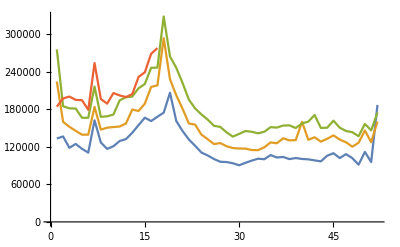

```mathematica
ListLinePlot[Delete[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Week"]&)->Last]/@GroupBy[Normal[worldByChecklist],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>],{4,18}]]
```

## Plotting Time Series

```mathematica
ListLinePlot[Partition[MapAt[DateValue[#+Quantity[1, "Days"],"Month"]&,Normal[worldByUserByMonth],{All,1}],12]]
```

{{{1,39424},{2,47033},{3,41795},{4,47393},{5,51458},{6,38203},{7,35758},{8,34705},{9,36479},{10,37168},{11,37506},{12,40826}},{{1,46283},{2,51344},{3,49866},{4,56977},{5,64451},{6,45457},{7,41412},{8,40415},{9,43077},{10,48518},{11,46329},{12,49760}},{{1,55970},{2,60266},{3,61002},{4,68373},{5,79231},{6,57047},{7,50896},{8,49801},{9,52046},{10,56257},{11,53339},{12,55715}}}

```mathematica
SortBy[First]/@MapAt[DateValue[#,"Month"]&,GroupBy[Normal[TimeSeriesShift[worldByUserByMonth,Quantity[1, "Days"]]],DateValue[#[[1]],"Year"]&],{All,All,1}]
```

<|2017→{{1,39424},{2,47033},{3,41795},{4,47393},{5,51458},{6,38203},{7,35758},{8,34705},{9,36479},{10,37168},{11,37506},{12,40826}},2018→{{1,46283},{2,51344},{3,49866},{4,56977},{5,64451},{6,45457},{7,41412},{8,40415},{9,43077},{10,48518},{11,46329},{12,49760}},2019→{{1,55970},{2,60266},{3,61002},{4,68373},{5,79231},{6,57047},{7,50896},{8,49801},{9,52046},{10,56257},{11,53339},{12,55715}},2020→{{1,63593},{2,72029},{3,68081},{4,79306}}|>

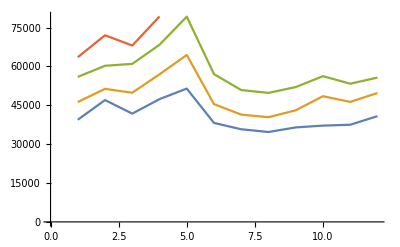

```mathematica
ListLinePlot[Values[SortBy[First]/@MapAt[DateValue[#,"Month"]&,GroupBy[Normal[TimeSeriesShift[worldByUserByMonth,Quantity[1, "Days"]]],DateValue[#[[1]],"Year"]&],{All,All,1}]]]
```

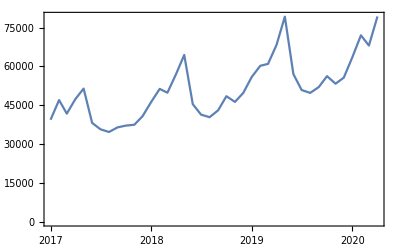

```mathematica
DateListPlot[worldByUserByMonth]
```

```mathematica
Normal[worldByUserByMonth]
```

{{Sat 31 Dec 2016 21:01:01GMT-4.,39424},{Tue 31 Jan 2017 21:01:01GMT-4.,47033},{Tue 28 Feb 2017 21:01:01GMT-4.,41795},{Fri 31 Mar 2017 21:01:01GMT-4.,47393},{Sun 30 Apr 2017 21:01:01GMT-4.,51458},{Wed 31 May 2017 21:01:01GMT-4.,38203},{Fri 30 Jun 2017 21:01:01GMT-4.,35758},{Mon 31 Jul 2017 21:01:01GMT-4.,34705},{Thu 31 Aug 2017 21:01:01GMT-4.,36479},{Sat 30 Sep 2017 21:01:01GMT-4.,37168},{Tue 31 Oct 2017 21:01:01GMT-4.,37506},{Thu 30 Nov 2017 21:01:01GMT-4.,40826},{Sun 31 Dec 2017 21:01:01GMT-4.,46283},{Wed 31 Jan 2018 21:01:01GMT-4.,51344},{Wed 28 Feb 2018 21:01:01GMT-4.,49866},{Sat 31 Mar 2018 21:01:01GMT-4.,56977},{Mon 30 Apr 2018 21:01:01GMT-4.,64451},{Thu 31 May 2018 21:01:01GMT-4.,45457},{Sat 30 Jun 2018 21:01:01GMT-4.,41412},{Tue 31 Jul 2018 21:01:01GMT-4.,40415},{Fri 31 Aug 2018 21:01:01GMT-4.,43077},{Sun 30 Sep 2018 21:01:01GMT-4.,48518},{Wed 31 Oct 2018 21:01:01GMT-4.,46329},{Fri 30 Nov 2018 21:01:01GMT-4.,49760},{Mon 31 Dec 2018 21:01:01GMT-4.,55970},{Thu 31 Jan 2019 21:01:01GMT-4.,60266},{Thu 28 Feb 2019 21:01:01GMT-4.,61002},{Sun 31 Mar 2019 21:01:01GMT-4.,68373},{Tue 30 Apr 2019 21:01:01GMT-4.,79231},{Fri 31 May 2019 21:01:01GMT-4.,57047},{Sun 30 Jun 2019 21:01:01GMT-4.,50896},{Wed 31 Jul 2019 21:01:01GMT-4.,49801},{Sat 31 Aug 2019 21:01:01GMT-4.,52046},{Mon 30 Sep 2019 21:01:01GMT-4.,56257},{Thu 31 Oct 2019 21:01:01GMT-4.,53339},{Sat 30 Nov 2019 21:01:01GMT-4.,55715},{Tue 31 Dec 2019 21:01:01GMT-4.,63593},{Fri 31 Jan 2020 21:01:01GMT-4.,72029},{Sat 29 Feb 2020 21:01:01GMT-4.,68081},{Tue 31 Mar 2020 21:01:01GMT-4.,79306}}

```mathematica
manuallyTranscribed={{39424,46283,55970,63593},{47033,51344,60266,72029},{41795,49866,61002,68081},{47393,56977,68373,79306},{51458,64451,79231},{38203,45457,57047},{35758,41412,50896},{34705,40415,49801},{36479,43077,52046},{37168,48518,56257},{37506,46329,53339},{40826,49760,55715}};
```

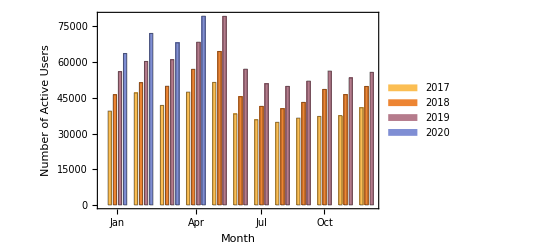

```mathematica
BarChart[manuallyTranscribed,ChartLabels->{{"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"},None},ChartLegends->{"2017","2018","2019","2020"},Frame->True,FrameLabel->{Style["Month",15],Style["Number of Active Users",15]}]
```

### World

#### Users per Month

```mathematica
DateListPlot[worldByUserByMonth,PlotRange->All]
```

-Graphics-

#### Absolute Numbers world

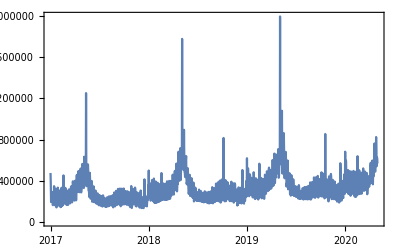

```mathematica
DateListPlot[worldByObservation,PlotRange->All]
```

#### Percentage Growth in Observations world

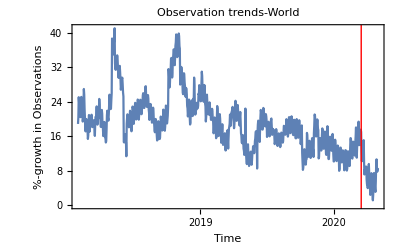

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByObservation,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Observations"},PlotLabel->"Observation trends-World"]
```

#### Percentage Growth in Checklists world

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByChecklist,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Checklists"},PlotTheme->"LargeLabels"]
```

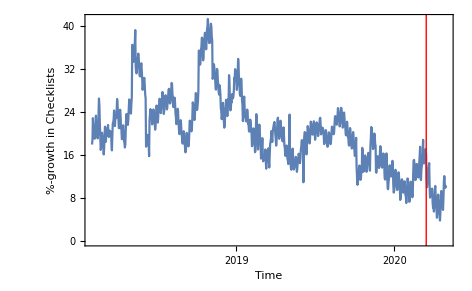
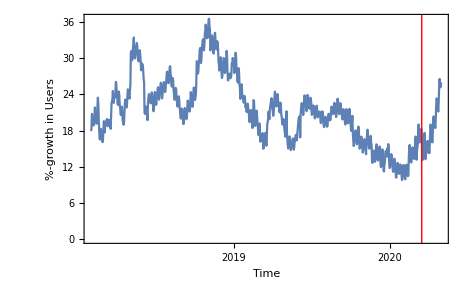

#### Percentage growth in Users

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,worldByUser,LinguisticAssistant],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Users"},PlotTheme->"LargeLabels"]
```

-Graphics-

### United States

#### Percentage growth in observations US

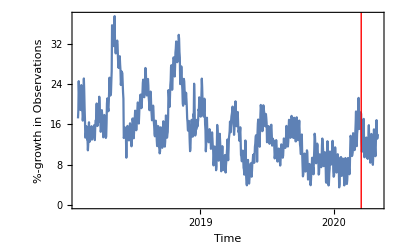

```mathematica
DateListPlot[MovingMap[(Last[#]-First[#])/First[#]*100&,MovingMap[Mean,USByObservation,Quantity[1, "Months"]],Quantity[1, "Years"]],Epilog->{Red,InfiniteLine[{DateObject[{2020, 3, 15}],0},{0,1}]},Frame->True,FrameLabel->{"Time","%-growth in Observations"}]
```

## Short eBird Dataset

```mathematica
eBirdFileStream= OpenRead["/Users/katjad/Documents/eBird/ebd_sampling_relApr-2020/ebd_sampling_relApr-2020.txt"]
```

InputStream[…]

```mathematica
eBirdLine=StringSplit[ReadLine[eBirdFileStream],"\t"]
```

{2009-07-17 11:57:41,United States,US,Massachusetts,US-MA,Plymouth,US-MA-023,,30,,,Landing Rd,L131261,P,41.9909210,-70.7253113,2002-10-29,07:00:00,obs18502,S949814,Stationary,P21,EBIRD,30,,,1,0}

```mathematica
Grid[MapIndexed[List,eBirdLine]]
```

LAST EDITED DATE | {1}
country | {2}
COUNTRY CODE | {3}
STATE | {4}
STATE CODE | {5}
COUNTY | {6}
COUNTY CODE | {7}
IBA CODE | {8}
BCR CODE | {9}
USFWS CODE | {10}
ATLAS BLOCK | {11}
LOCALITY | {12}
LOCALITY ID | {13}
LOCALITY TYPE | {14}
LATITUDE | {15}
LONGITUDE | {16}
OBSERVATION DATE | {17}
TIME OBSERVATIONS STARTED | {18}
OBSERVER ID | {19}
SAMPLING EVENT IDENTIFIER | {20}
PROTOCOL TYPE | {21}
PROTOCOL CODE | {22}
PROJECT CODE | {23}
DURATION MINUTES | {24}
EFFORT DISTANCE KM | {25}
EFFORT AREA HA | {26}
NUMBER OBSERVERS | {27}
ALL SPECIES REPORTED | {28}
GROUP IDENTIFIER | {29}
TRIP COMMENTS | {30}

```mathematica
eBirdFileStream= OpenRead["/Users/katjad/Documents/eBird/ebd_sampling_relApr-2020/ebd_sampling_relApr-2020.txt"];
eBirdLine=StringSplit[ReadLine[eBirdFileStream],"\t"];
eBirdDateCounts = <||>;
n = 0;
Module[{lines,date},
	While[lines=ReadList[eBirdFileStream,Record,10000];lines =!= {},
		If[Divisible[n++,100], Echo[n]];
		Function[line,
			date= StringTake[StringSplit[line,"\t"][[17]],10];
			If[
				!KeyExistsQ[eBirdDateCounts,date],
				eBirdDateCounts[date]=1,
				eBirdDateCounts[date]++]
		]/@lines
	]
];
Close[eBirdFileStream];
```

Above started at: 11:40

```mathematica
Now
```

Mon 29 Jun 2020 00:05:20GMT-4.

```mathematica
eBirdTimeSeries=TimeSeries[KeyMap[DateObject[#]&,eBirdDateCounts]]
```

TimeSeries[…]

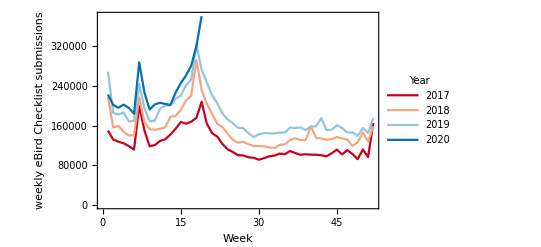

```mathematica
ListLinePlot[Delete[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(DateValue[#[[1]],"Week"]&)->Last]/@GroupBy[Normal[eBirdTimeSeries],DateValue[#[[1]],"Year"]&],{2}],Range[2017,2020],<||>],{4,20}],Frame->True,FrameLabel->{"Week","weekly eBird Checklist submissions"},PlotLegends->LineLegend[{"2017","2018","2019","2020"},LegendLabel->"Year"],PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4]]
```

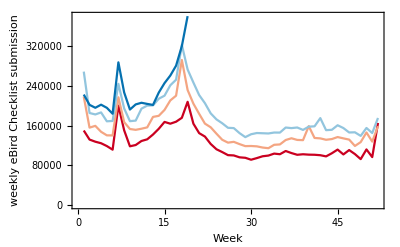
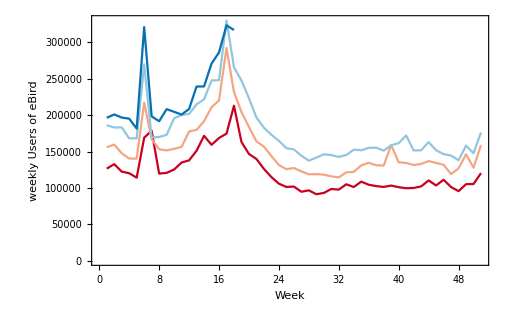

```mathematica
Close[eBirdFileStream]
```

/Users/katjad/Documents/eBird/ebd_sampling_relApr-2020/ebd_sampling_relApr-2020.txt

```mathematica
(*Export["~/Documents/iNaturalist/eBirdByChecklist.mx",eBirdDateCounts]*)
```

~/Documents/iNaturalist/eBirdByChecklist.mx

```mathematica
parseEBirdDateObject[do_]:=DateObject[ToExpression/@StringSplit[do,"-"]]
```

```mathematica
parseEBirdDateObject["2017-10-29"]
```

Day: Sun 29 Oct 2017

```mathematica
eBirdFileStream= OpenRead["/Users/katjad/Documents/eBird/ebd_sampling_relApr-2020/ebd_sampling_relApr-2020.txt"];
eBirdLine=StringSplit[ReadLine[eBirdFileStream],"\t"];
eBirdUserCounts = <||>;
userIDs = <||>;
n = 0;
getWeek[do_?DateObjectQ]:=Floor[(UnixTime[do]-UnixTime[DateObject[{DateValue[do,"Year"],1,1}]])/(7*24*60*60)]
parseEBirdDateObject[do_]:=DateObject[ToExpression/@StringSplit[do,"-"]]
Module[{lines,date,lineList,exactDate,user},
	While[lines=ReadList[eBirdFileStream,Record,10000];lines =!= {},
		If[Divisible[n++,100], Echo[n]];
		Function[line,
			lineList=StringSplit[line,"\t"];
			exactDate = parseEBirdDateObject[StringTake[lineList[[17]],10]];
			date = {DateValue[exactDate,"Year"], getWeek[exactDate]};
			user = lineList[[19]];
			If[
				!KeyExistsQ[userIDs,date],
				eBirdUserCounts[date]=1;
				userIDs[date]={user},
				If[
					MemberQ[userIDs[date],user],
					Nothing,
					Append[userIDs[date],user];
					eBirdUserCounts[date]++]]
		]/@lines
	]
];
Close[eBirdFileStream];
```

```mathematica
eBirdUserCounts
```

<|{2002,19}→10421,{2002,43}→5974,{2001,18}→9412,{2002,44}→5646,{2002,4}→4816,{2002,45}→5196,{2000,35}→5042,{2002,2}→5506,{2002,3}→5130,{2002,33}→5181,{2002,46}→5168,{2002,47}→5530,{2002,15}→8712,{2012,48}→35500,{2002,48}→4546,{2002,20}→9622,{2002,34}→5747,{2002,49}→4824,{2003,3}→5299,{2003,4}→5471,{2002,50}→4440,{2002,51}→5594,{2003,0}→8170,7906,{1880,6}→1,{1879,42}→1,{1885,50}→1,{1898,32}→1,{1876,25}→1,{1874,34}→1,{1882,0}→2,{1882,27}→1,{1881,49}→1,{1882,45}→1,{1921,6}→2,{1897,27}→1,{1871,32}→1,{1882,38}→1,{1800,40}→1,{1869,23}→1,{1905,33}→2,{1881,26}→1,{1919,1}→1,{1880,46}→1,{1868,35}→1,{1825,30}→1|>
 |  |  |  |

```mathematica
GroupBy[(#[[1]][[2]]&)->Last]/@GroupBy[Normal[eBirdUserCounts],#[[1]][[1]]&]
```

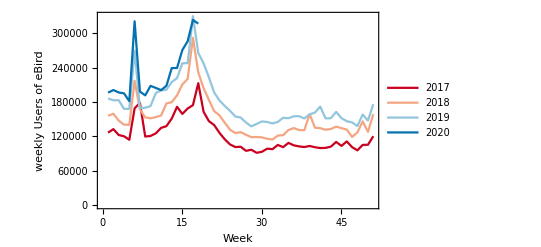

```mathematica
ListLinePlot[Delete[Delete[Delete[Delete[Lookup[#,Range[1,52]]&/@Lookup[Map[Total,GroupBy[(#[[1]][[2]]&)->Last]/@GroupBy[Normal[eBirdUserCounts],#[[1]][[1]]&],{2}],Range[2017,2020],<||>],{1,-1}],{2,-1}],{3,-1}],{4,-1}],Frame->True,FrameLabel->{"Week","weekly Users of eBird"},PlotLegends->{"2017","2018","2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",4]]
```